# 医学生物学分野における引用グラフの成長

## 要旨

PubMedの3000万件を超える収録記事を対象として、レファレンス情報を抽出し、レファレンスネットワークの構造変化を75年間にわたり俯瞰する。

## 1. 背景

大規模な引用関係の分析は、雑誌間あるいは組織間等のある程度まとまったレベルでの関係に注目されることが多かった。これは、論文を要素とする大規模な引用関係をそのまま分析するには粒度が小さすぎる（要素が多すぎる）ためである。あるいは、この問題の回避には、論文をクラスタリングする方法があり、引用関係や研究テーマでの分類が可能であるが、明確な粒度の線引きは簡単ではない。それでも、妥当な粒度を見つけ出し分析した研究は多い。Leydesdorff[1,2,3,4]は雑誌間の関係マップを構築・調査した。天野ら[5,6]は医学生物学雑誌の大規模クラスタリングを行い、分野間の引用関係を明らかにしている。近年ではLiら[7]が長期にわたる引用の特徴を、2300万論文をグループ化して調査した。一方、これらはどちらかと言えば短期間の分析であり、長期にわたる引用ネットワークの分析は非常に少ない。その理由としては、分類単位である雑誌や組織や分野という視点そのものが、長期間においては変化しうるものだからである。そこで本研究では、論文単位のレファレンスネットワークそのものを直接の対象としつつ、このようなクラスタリングの問題が最小となる方法を採用し、長期のネットワークの動態変化を分析する。方法の一つとして、各クラスを、純粋なネットワーク構造にのみ注目して分離を行えば、これが実現できると考える。すなわちグラフの分割をWeakly-connected component graphを単位とすることで対応し、時間軸においてはこのWeakly-connected component graph の結合構造に注目しその変化を明らかにする。

## 2. 目的

論文単位の引用ネットワークが長期的にどのように変化するのかを、Weakly-connected component graphに注目し、さまざまなネットワーク指標を用いて観察する。

## 3. マテリアル

### 3.1 データ

FTP版のPubmed baseline (2023)[8]を利用する。レファレンスネットワークの構成は、PubMedに収録されている論文のうち出版年が1946-2020のものに記載されるレファレンスを対象とし、次に述べる方法で「世代」を構築する。

本研究で用いた2023年のFTP版PubMed annual baselineの概要を表1に示す。わずかに2024年の論文も含まれている。

図1に出版年ごとの論文収録数を示す。1945年から明確な増加が見られる。

表 2

PubMed annual baselineのレコード数

論文数 | 雑誌数 | 最初の論文出版年 | 最後の論文出版年
36,555,430 | 36,943 | 1781 | 2024

図1に出版年ごとの論文収録数を示す。1945年から明確な増加が見られる。

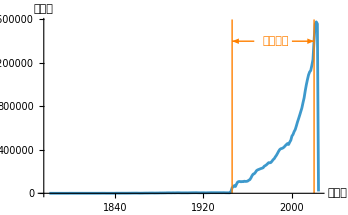

図1

PubMed annual baselineの登録論文数の推移

### 3.2 世代の構成

本研究ではレファレンスネットワーク全体がどのように成長するかを見るため、世代を累積的に構成する。これを「累積世代」と称する。まず、1946-2020年の出版論文をオーバーラップなしの5年ごとの出版に分け、これらの論文集合のレファレンス情報から、15層のレファレンスネットワークを構成する。次に、第一層から累積的に一層ずつ層を結合し、第15累積世代では1~15層が結合されたレファレンスネットワークとなるようにネットワークの累積世代を構成する。対象となる記事のタイプは全てである。また、この構成方法では1946年より前に出版された論文も対象に含まれる。

### 3.3 Weakly-connected component graph

本研究ではレファレンスネットワーク構造の変化を計量的に観察する。このため、ネットワーク全体をより下位のネットワークに分け、その変化を観察する。レファレンスネットワーク全体の下位構造として想定されるものには、引用関係、共著関係によるネットワークの分割や、テーマによる分類等があるが、本研究では引用ネットワークを最も直接的かつ明確に分ける単位として弱連結グラフ（Weakly-connected component graph: WCC）を採用する。前述の方法にて累積世代グラフを構築したのち、前世代のWCCと当該世代のWCCを繋ぐリンク等に注目し分析を行う。

## 4. 結果

### 4.1 レファレンスネットワーク構造の変化

累積世代ごとのレファレンスネットワーク全体に関してのエッジ総数と複雑度を図2に示す。複雑度については、ノード間の距離に無限大が存在しても発散しないサイクロマティック複雑度(<エッジ数> - <ノード数> + 2 <コンポーネント数>)[9]を用いた。加えて、累積世代ごとのWCCのノード総数、最大WCCのノード数、WCC数および孤立ノード数を、同じく図2に示す。これらはすべて増加傾向にある。なお、WCCノード総数の70%以上を最大WCCのノードが占めている。

また、以上の属性の増加率（微分）を図3に示す。これによれば、全ネットワークにおけるエッジ総数と複雑度は加速度的な上昇を見せている。WCCノード総数と最大WCCノード数も同じく加速度的な増加を見せている。WCC数の増加率については増減があるものの、その変化は一定の範囲内に見られる。孤立ノード数は上昇傾向ではあるものの、増加率については1946-1995年累積世代以降低くなっている。

次に、総WCCノードにおける最大WCCノード数の占有率、ネットワークの総ノードにおける最大WCCノード数の占有率およびネットワークの総ノードにおける孤立ノードの占有率を図4に示す。これによれば最大WCCはその占有率を増加させ続けており、孤立ノードの占有率は減少傾向にある。

-Graphics-

図2 全ネットワークおよびWCCに関する基本的な統計値

-Graphics-

図3 全ネットワークおよびWCCに関する基本的な統計値の増加率

-Graphics-

図4 各種ノードの占有率

### 4.2 レファレンスネットワークの成長

#### 4.2.1 ネットワークの結合要素

ここでは、累積世代間でどのようにWCCが結合されるかを見るため、異なるWCCを結合する引用に注目する。表1に結合によるWCC数の変化を示す。この表より、結合されるWCC数は累積世代ごとに増加傾向にある。この際、結合後には該当するWCC数は減少するが、この効果を「前世代WCC数」/「結合後WCC数」と定義し、「圧縮率」と呼ぶこととする。この圧縮率について何らかの傾向は見られなかった。また、新規に発生した引用による結合の効率を、(「結合が発生したWCC数」/「結合後WCC数」) / 「前世代WCC数」と定義し、すべてが結合された場合に1（100%）となるよう調整した。この結合効率には減少傾向が見られる。さらに、WCCの結合に寄与する論文の割合を「前世代WCCを結合する論文数」/「論文総数」と定義した。この割合には減少傾向が見られる。

表1 WCCの結合およびメンバー数の変化

累積世代 | 新規に発生した引用数 | 新規に発生した引用に関し
異なる前世代WCCを結合する
論文の数 [a] | 論文総数 [b] | WCC結合に寄与する
論文の割合(%)
[a]/[b] | 新規に発生した引用により
結合が発生した前世代WCC数[1] | 新規に発生した引用による
結合後のWCG数[2] | 前世代WCC数[3] | WCCの結合による
圧縮率 [3]/[2] | WCCの結合効率(%)
([1]/[2])/[3]
1946-1955 | 148555 | 1632 | 106865 | 1.53 | 1280 | 909 | 2353 | 2.59 | 0.06
1946-1960 | 291655 | 1942 | 230664 | 0.84 | 1485 | 1185 | 3851 | 3.25 | 0.033
1946-1965 | 445022 | 1717 | 387646 | 0.44 | 1297 | 1070 | 4624 | 4.32 | 0.026
1946-1970 | 818629 | 1937 | 635815 | 0.3 | 1411 | 1133 | 5729 | 5.06 | 0.022
1946-1975 | 1369688 | 2240 | 991194 | 0.23 | 1549 | 1306 | 7020 | 5.38 | 0.017
1946-1980 | 1998678 | 2520 | 1452803 | 0.17 | 1716 | 1500 | 8446 | 5.63 | 0.014
1946-1985 | 2821649 | 2480 | 2022734 | 0.12 | 1683 | 1478 | 9401 | 6.36 | 0.012
1946-1990 | 4022714 | 2438 | 2761367 | 0.09 | 1553 | 1392 | 10026 | 7.2 | 0.011
1946-1995 | 5715688 | 2345 | 3715190 | 0.06 | 1450 | 1310 | 10687 | 8.16 | 0.01
1946-2000 | 6095490 | 1603 | 4704818 | 0.03 | 1147 | 1048 | 11361 | 10.84 | 0.01
1946-2005 | 9616785 | 2553 | 6388248 | 0.04 | 1508 | 1353 | 12147 | 8.98 | 0.009
1946-2010 | 27854672 | 6243 | 9604916 | 0.06 | 2576 | 2407 | 13000 | 5.4 | 0.008
1946-2015 | 63696093 | 11124 | 14351433 | 0.08 | 3404 | 3235 | 13398 | 4.14 | 0.008
1946-2020 | 98878679 | 11676 | 20271870 | 0.06 | 3472 | 3255 | 13643 | 4.19 | 0.008

#### 4.2.2 WCCのサイズと結合強度（結合数）

## 考察・まとめ

## 参考

Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Docu- mentation. 2004, Vol. 60, No. 4, p. 371-427.

Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

Leydesdorf L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports? Journal of the American Society for Information Science and Tech- nology. 2006, Vol. 57, No. 5, p. 601-613.

天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

Li

https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2024.07.01)

McCabe, T. J. (1976). A Complexity Measure. IEEE Transactions on Software Engineering, SE-2(4), 308–320.

## 検討

ノード数（N）☑️

エッジ数（M）☑️

グラフ直径（最大次数）-> メモリーオーバーにより計算不可

平均次数: M / N

密度: M / (N * (N-1))

グラフ複雑性☑️

増加率のplot

#### 研究テーマ

検討事項：WCCを統合するリンク（論文）の特性を研究テーマで見る。
(0)累積世代内のテーマ
(1)累積世代間のリンクテーマの推移 -> リンク論文を抽出しているか確認する
(2)WCC間のリンクテーマの差異（上位25パーセンタイルのWCC）

## プログラム

複雑性定義の案

graphRedundancyComplexity[g_Graph] := Module[{vc, ec, ecmean, etp},
  vc = VertexCount[g] // N;
  ec = EdgeCount[g] // N;
  ecmean = ec/(vc^2);
  etp = Entropy[AdjacencyMatrix[g] // Flatten] // N;
  (vc) (vc^ecmean) Exp[etp]
  ]